```mathematica
Clear["Global`*"];
r1[x1_,y1_] := {x1, y1};
r2[x2_,y2_] := {x2, y2};
r3[x3_,y3_] := {x3, y3};
r4[x4_,y4_] := {x4, y4};
(*define everything as functions of r1,r2 or t*)
r12[x1_,y1_, x2_, y2_]:=Norm[r1[x1,y1]-r2[x2,y2]];
r13[x1_,y1_, x3_, y3_]:=Norm[r1[x1,y1]-r3[x3,y3]];
r14[x1_,y1_, x4_, y4_]:=Norm[r1[x1,y1]-r4[x4,y4]];
r23[x2_,y2_, x3_, y3_]:=Norm[r2[x2,y2]-r3[x3,y3]];
r24[x2_,y2_, x4_, y4_]:=Norm[r2[x2,y2]-r4[x4,y4]];
r34[x3_,y3_, x4_, y4_] :=Norm[r3[x3,y3]-r4[x4,y4]];
(*m is a mass matrix, not a vector*)
m=ArrayFlatten[{{m1*IdentityMatrix[2],{{0,0},{0,0}}, {{0,0},{0,0}}, {{0,0},{0,0}}},{{{0,0},{0,0}},m2*IdentityMatrix[2],{{0,0},{0,0}}, {{0,0},{0,0}}}, {{{0,0},{0,0}},{{0,0},{0,0}},m3*IdentityMatrix[2], {{0,0},{0,0}}}, {{{0,0},{0,0}},{{0,0},{0,0}}, {{0,0},{0,0}}, m4*IdentityMatrix[2]}}];


M11 := IdentityMatrix[2]/(6*π*η*a1);
(*(r1-r2)*(r1-r2) is suposed to be a dyadic product*)
(*I think you also had a typo in ((x1[t]-x2[t])*(x2[t]-x1[t]))*)
M12[x1_,y1_, x2_, y2_]:= 1/(8*π*η*r12[x1,y1, x2,y2])*(IdentityMatrix[2]+TensorProduct[(r1[x1,y1]-r2[x2,y2]),(r1[x1,y1]-r2[x2,y2])]/r12[x1,y1, x2,y2]^2);
M13[x1_,y1_, x3_, y3_]:= 1/(8*π*η*r13[x1,y1, x3,y3])*(IdentityMatrix[2]+TensorProduct[(r1[x1,y1]-r3[x3,y3]),(r1[x1,y1]-r3[x3,y3])]/r13[x1,y1, x3,y3]^2);
M14[x1_,y1_, x4_, y4_]:= 1/(8*π*η*r14[x1,y1, x4,y4])*(IdentityMatrix[2]+TensorProduct[(r1[x1,y1]-r4[x4,y4]),(r1[x1,y1]-r4[x4,y4])]/r14[x1,y1, x4,y4]^2);





M21[x2_,y2_, x1_, y1_] := 1/(8*π*η*r12[x1,y1, x2,y2])*(IdentityMatrix[2]+TensorProduct[(r2[x2,y2]-r1[x1,y1]),(r2[x2,y2]-r1[x1,y1])]/r12[x1,y1, x2,y2]^2);

M22 := IdentityMatrix[2]/(6*π*η*a2);


M23[x2_,y2_, x3_, y3_] := 1/(8*π*η*r23[x2,y2, x3, y3])*(IdentityMatrix[2]+TensorProduct[(r2[x2,y2]-r3[x3,y3]),(r2[x2,y2]-r3[x3,y3])]/r23[x2,y2, x3,y3]^2);
M24[x2_,y2_, x4_, y4_] := 1/(8*π*η*r24[x2,y2, x4,y4])*(IdentityMatrix[2]+TensorProduct[(r2[x2,y2]-r4[x4,y4]),(r2[x2,y2]-r4[x4,y4])]/r24[x2,y2, x4,y4]^2);





M31[x3_,y3_, x1_, y1_] := 1/(8*π*η*r13[x1,y1, x3,y3])*(IdentityMatrix[2]+TensorProduct[(r3[x3,y3]-r1[x1,y1]),(r3[x3,y3]-r1[x1,y1])]/r13[x1,y1, x3,y3]^2);


M32[x3_,y3_, x2_, y2_] := 1/(8*π*η*r23[x2,y2, x3,y3])*(IdentityMatrix[2]+TensorProduct[(r3[x3,y3]-r2[x2,y2]),(r3[x3,y3]-r2[x2,y2])]/r23[x2,y2, x3,y3]^2);


M33:= IdentityMatrix[2]/(6*π*η*a3);

M34[x3_,y3_, x4_, y4_] := 1/(8*π*η*r34[x3,y3, x4,y4])*(IdentityMatrix[2]+TensorProduct[(r3[x3,y3]-r4[x4,y4]),(r3[x3,y3]-r4[x4,y4])]/r34[x3,y3, x4,y4]^2);



M41[x4_,y4_, x1_, y1_] := 1/(8*π*η*r14[x1,y1, x4,y4])*(IdentityMatrix[2]+TensorProduct[(r4[x4,y4]-r1[x1,y1]),(r4[x4,y4]-r1[x1,y1])]/r14[x1,y1, x4,y4]^2);


M42[x4_,y4_, x2_, y2_]:= 1/(8*π*η*r24[x2,y2, x4,y4])*(IdentityMatrix[2]+1/r24[x2,y2, x4,y4]^2 TensorProduct[(r4[x4,y4]-r2[x2,y2]),(r4[x4,y4]-r2[x2,y2])]);


M43[x4_,y4_, x3_, y3_] := 1/(8*π*η*r34[x3,y3, x4, y4])*(IdentityMatrix[2]+TensorProduct[(r4[x4,y4]-r3[x3,y3]),(r4[x4,y4]-r3[x3,y3])]/r34[x3,y3, x4,y4]^2);

M44 :=IdentityMatrix[2]/(6*π*η*a4);





M [x1_,y1_, x2_, y2_, x3_, y3_, x4_, y4_]:= ArrayFlatten[{{M11, M12[x1,y1,x2,y2], M13[x1,y1,x3,y3], M14[x1,y1,x4,y4]},{M21[x2,y2,x1,y1], M22, M23[x2,y2,x3,y3], M24[x2,y2,x4,y4]}, {M31[x3,y3,x1,y1], M32[x3,y3,x2,y2], M33, M34[x3,y3,x4,y4]}, {M41[x4,y4,x1,y1], M42[x4,y4,x2,y2], M43[x4,y4,x3,y3], M44}}];


F12[x1_,y1_, x2_, y2_,t_]:= Fa*Cos[2*π * f *t-(ϕ/2)]*((r1[x1,y1]-r2[x2,y2])/r12[x1,y1,x2,y2]);
F21[x1_,y1_, x2_, y2_, t_] := Fa*Cos[2*π * f *t - (ϕ/2)]*((r2[x2,y2]-r1[x1,y1])/r12[x1,y1,x2,y2]);


F34[x3_,y3_, x4_, y4_,t_]:= Fa*Cos[2*π * f *t+(ϕ/2)]*((r3[x3,y3]-r4[x4,y4])/r34[x3,y3,x4,y4]);
F43[x4_,y4_, x3_, y3_, t_] := Fa*Cos[2*π * f *t+(ϕ/2)]*((r4[x4,y4]-r3[x3,y3])/r34[x3,y3,x4,y4]);


(*Fa, aka the force amplitude, was renamed (used to be called F) since it was coinciding with the general force function, also called F:*)
F [x1_,y1_, x2_, y2_, x3_, y3_, x4_, y4_,t_]:= Flatten[{F12[x1,y1,x2,y2,t], F21[x1,y1,x2,y2,t], F34[x3, y3, x4, y4, t], F43[x4, y4, x3, y3, t]}];
(**(x1[t]-x2[t])*)
G12[x1_,y1_, x2_, y2_]:=-k *(r12[x1,y1,x2,y2]-L)*(r1[x1,y1]-r2[x2,y2])/r12[x1,y1,x2,y2]; 
G21[x1_,y1_, x2_, y2_]:=-k *(r12[x1,y1,x2,y2]-L)*(r2[x2,y2]-r1[x1,y1])/r12[x1,y1,x2,y2]; 
G34[x3_,y3_, x4_, y4_]:=-k *(r34[x3,y3,x4,y4]-L)*(r3[x3,y3]-r4[x4,y4])/r34[x3,y3,x4,y4]; 
G43[x3_,y3_, x4_, y4_]:=-k *(r34[x3,y3,x4,y4]-L)*(r4[x4,y4]-r3[x3,y3])/r34[x3,y3,x4,y4]; 
G[x1_,y1_, x2_, y2_, x3_, y3_, x4_, y4_]:=Flatten[{G12[x1,y1,x2,y2], G21[x1,y1,x2,y2], G34[x3, y3, x4, y4], G43[x3, y3, x4, y4]}];
(*input paramters*)
a1 = 5;
a2 = 8;
a3 = a1;
a4 = a2;
η = 1/6;
f =0.2*10^-3;
Fa = 0.05;
k = 1/200;
L = 28;
ρs = 8;
m1 = 4/3*π*a1^3*ρs;
m2 = 4/3*π*a2^3*ρs;
m3 = 4/3*π*a3^3*ρs;
m4 = 4/3*π*a4^3*ρs;
(*τ is the period length*)
τ=1/f;
(* ϕ is the phase shit between swimmer 1 and 2, 2 is ϕ ahead of 1*)
ϕ = 0;
```

```mathematica
LHS[x1_,y1_,x2_,y2_, x3_, y3_, x4_, y4_] := Flatten[D[{{x1,y1},{x2,y2}, {x3,y3},{x4,y4}},t]] 
RHS[x1_,y1_,x2_,y2_, x3_, y3_, x4_, y4_,t_] := M [x1,y1, x2, y2, x3, y3, x4, y4].(F[x1, y1, x2, y2, x3, y3, x4, y4, t]+G[x1, y1, x2, y2, x3, y3, x4, y4]-m.D[{x1,y1,x2,y2, x3, y3, x4, y4},{t,2}])
```

```mathematica
sol3 = NDSolve[{LHS[x1[t],y1[t],x2[t],y2[t], x3[t], y3[t], x4[t], y4[t]]==RHS[x1[t],y1[t],x2[t],y2[t], x3[t], y3[t], x4[t], y4[t],t],(*{x1[t],y1[t],x2[t],y2[t]},*) { x1[0],y1[0],x2[0],y2[0], x3[0], y3[0], x4[0], y4[0]}=={-L,5,0,5, -L/2, (5+0.5L), -L/2, (5+1.5L)}, { x1'[0],y1'[0],x2'[0],y2'[0], x3'[0], y3'[0], x4'[0], y4'[0]}=={0,0,0,0, 0, 0, 0, 0}},{x1,y1,x2,y2, x3, y3, x4, y4},{t,0.01,100τ}, Method->{"EquationSimplification"->"Residual"}]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],x2→InterpolatingFunction[…],y2→InterpolatingFunction[…],x3→InterpolatingFunction[…],y3→InterpolatingFunction[…],x4→InterpolatingFunction[…],y4→InterpolatingFunction[…]}}

```mathematica
NIntegrate[Evaluate[1/τ*{(Norm[{x1'[t],y1'[t]}]+Norm[{x2'[t],y2'[t]}])/2}/.sol3],{t,98τ,99τ}]



NIntegrate[Evaluate[1/τ*{(Norm[{x3'[t],y3'[t]}]+Norm[{x4'[t],y4'[t]}])/2}/.sol3],{t,98τ,99τ}]
```

{{0.00128251}}

{{0.00107065}}

```mathematica
m
```

{{(4000 π)/3,0,0,0,0,0,0,0},{0,(4000 π)/3,0,0,0,0,0,0},{0,0,(16384 π)/3,0,0,0,0,0},{0,0,0,(16384 π)/3,0,0,0,0},{0,0,0,0,m3,0,0,0},{0,0,0,0,0,m3,0,0},{0,0,0,0,0,0,m4,0},{0,0,0,0,0,0,0,m4}}

```mathematica
M [x1,y1, x2, y2, x3, y3, x4, y4]
```

{{1/(5 π),0,3/(56 π),0,3/(112 π),0,1/(56 π),0},{0,1/(5 π),0,3/(112 π),0,3/(224 π),0,1/(112 π)},{3/(2 π r[-28,0,0,0]),0,1/(8 π),0,3/(56 π),0,3/(112 π),0},{0,3/(4 π r[-28,0,0,0]),0,1/(8 π),0,3/(112 π),0,3/(224 π)},{3/(112 π),0,3/(56 π),0,1/(5 π),0,3/(56 π),0},{0,3/(224 π),0,3/(112 π),0,1/(5 π),0,3/(112 π)},{1/(56 π),0,3/(112 π),0,3/(56 π),0,1/(8 π),0},{0,1/(112 π),0,3/(224 π),0,3/(112 π),0,1/(8 π)}}

```mathematica
F[x1, y1, x2, y2, x3, y3, x4, y4, t]
```

{-0.05 Cos[0.00125664 t],0.,0.05 Cos[0.00125664 t],0.,-0.05 Cos[0.00125664 t],0.,0.05 Cos[0.00125664 t],0.}

```mathematica
M [x1,y1, x2, y2, x3, y3, x4, y4].F[x1, y1, x2, y2, x3, y3, x4, y4, t]
```

{0.-0.00247259 Cos[0.00125664 t],0.,0.+0.00156313 Cos[0.00125664 t]-(0.0238732 Cos[0.00125664 t])/r[-28,0,0,0],0.,0.-0.00190418 Cos[0.00125664 t],0.,0.+0.00127892 Cos[0.00125664 t],0.}

```mathematica
G[x1, y1, x2, y2, x3, y3, x4, y4]
```

{0,0,0,0,0,0,0,0}

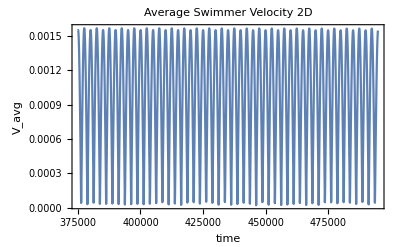

```mathematica
Plot[Evaluate[{(Norm[{x1'[t],y1'[t]}]+Norm[{x2'[t],y2'[t]}])/2}/.sol3],{t,75τ, 99τ},PlotRange->All, AxesStyle->Black,Frame->True,FrameStyle->Black,PlotLabel->Style["Average Swimmer Velocity 2D", Black], FrameLabel->{"time","V_avg"}]
```

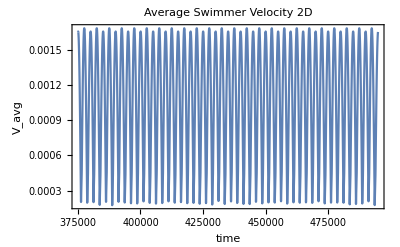

{{0.000989559}}

```mathematica
Plot[Evaluate[{(Norm[{x3'[t],y3'[t]}]+Norm[{x4'[t],y4'[t]}])/2}/.sol3],{t,75τ, 99τ},PlotRange->All, AxesStyle->Black,Frame->True,FrameStyle->Black,PlotLabel->Style["Average Swimmer Velocity 2D", Black], FrameLabel->{"time","V_avg"}]
```

```mathematica
dlist=Subdivide[0.5L,10L,20]
velListnum1=ConstantArray[Null,{Length[dlist]}]
velListnum2=ConstantArray[Null,{Length[dlist]}]
```

{14.,27.3,40.6,53.9,67.2,80.5,93.8,107.1,120.4,133.7,147.,160.3,173.6,186.9,200.2,213.5,226.8,240.1,253.4,266.7,280.}

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Do[D3=dlist[[i]];
sol3 = NDSolve[{LHS[x1[t],y1[t],x2[t],y2[t], x3[t], y3[t], x4[t], y4[t]]==RHS[x1[t],y1[t],x2[t],y2[t], x3[t], y3[t], x4[t], y4[t],t],(*{x1[t],y1[t],x2[t],y2[t]},*) { x1[0],y1[0],x2[0],y2[0], x3[0], y3[0], x4[0], y4[0]}=={-L,5,0,5, -0.5L, (5+D3), -0.5L, (5+D3+L)}, { x1'[0],y1'[0],x2'[0],y2'[0], x3'[0], y3'[0], x4'[0], y4'[0]}=={0,0,0,0, 0, 0, 0, 0}},{x1,y1,x2,y2, x3, y3, x4, y4},{t,0.01,100τ}, Method->{"EquationSimplification"->"Residual"}];
velListnum1[[i]]={NIntegrate[Evaluate[1/τ*{(Norm[{x1'[t],y1'[t]}]+Norm[{x2'[t],y2'[t]}])/2}/.sol3],{t,98τ,99τ}][[1]]}; ,{i,1,Length[dlist]}]
```

```mathematica
Flatten[velListnum1]
```

NIntegrate::inumr: The integrand 0.0001 (√(Abs[x1'[t]]^2+Abs[y1'[t]]^2)+√(Abs[x2'[t]]^2+Abs[y2'[t]]^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{490000,495000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{NIntegrate[0.0001 (√(Abs[x1'[t]]^2+Abs[y1'[t]]^2)+√(Abs[x2'[t]]^2+Abs[y2'[t]]^2)),{t,98 τ,99 τ}],NIntegrate[0.0001 (√(Abs[x1'[t]]^2+Abs[y1'[t]]^2)+√(Abs[x2'[t]]^2+Abs[y2'[t]]^2)),{t,98 τ,99 τ}],NIntegrate[0.0001 (√(Abs[x1'[t]]^2+Abs[y1'[t]]^2)+√(Abs[x2'[t]]^2+Abs[y2'[t]]^2)),{t,98 τ,99 τ}],NIntegrate[0.0001 (√(Abs[x1'[t]]^2+Abs[y1'[t]]^2)+√(Abs[x2'[t]]^2+Abs[y2'[t]]^2)),{t,98 τ,99 τ}],NIntegrate[0.0001 (√(Abs[x1'[t]]^2+Abs[y1'[t]]^2)+√(Abs[x2'[t]]^2+Abs[y2'[t]]^2)),{t,98 τ,99 τ}],NIntegrate[0.0001 (√(Abs[x1'[t]]^2+Abs[y1'[t]]^2)+√(Abs[x2'[t]]^2+Abs[y2'[t]]^2)),{t,98 τ,99 τ}],NIntegrate[0.0001 (√(Abs[x1'[t]]^2+Abs[y1'[t]]^2)+√(Abs[x2'[t]]^2+Abs[y2'[t]]^2)),{t,98 τ,99 τ}],NIntegrate[0.0001 (√(Abs[x1'[t]]^2+Abs[y1'[t]]^2)+√(Abs[x2'[t]]^2+Abs[y2'[t]]^2)),{t,98 τ,99 τ}],NIntegrate[0.0001 (√(Abs[x1'[t]]^2+Abs[y1'[t]]^2)+√(Abs[x2'[t]]^2+Abs[y2'[t]]^2)),{t,98 τ,99 τ}],NIntegrate[0.0001 (√(Abs[x1'[t]]^2+Abs[y1'[t]]^2)+√(Abs[x2'[t]]^2+Abs[y2'[t]]^2)),{t,98 τ,99 τ}],NIntegrate[0.0001 (√(Abs[x1'[t]]^2+Abs[y1'[t]]^2)+√(Abs[x2'[t]]^2+Abs[y2'[t]]^2)),{t,98 τ,99 τ}],NIntegrate[0.0001 (√(Abs[x1'[t]]^2+Abs[y1'[t]]^2)+√(Abs[x2'[t]]^2+Abs[y2'[t]]^2)),{t,98 τ,99 τ}],NIntegrate[0.0001 (√(Abs[x1'[t]]^2+Abs[y1'[t]]^2)+√(Abs[x2'[t]]^2+Abs[y2'[t]]^2)),{t,98 τ,99 τ}],NIntegrate[0.0001 (√(Abs[x1'[t]]^2+Abs[y1'[t]]^2)+√(Abs[x2'[t]]^2+Abs[y2'[t]]^2)),{t,98 τ,99 τ}],NIntegrate[0.0001 (√(Abs[x1'[t]]^2+Abs[y1'[t]]^2)+√(Abs[x2'[t]]^2+Abs[y2'[t]]^2)),{t,98 τ,99 τ}],NIntegrate[0.0001 (√(Abs[x1'[t]]^2+Abs[y1'[t]]^2)+√(Abs[x2'[t]]^2+Abs[y2'[t]]^2)),{t,98 τ,99 τ}],NIntegrate[0.0001 (√(Abs[x1'[t]]^2+Abs[y1'[t]]^2)+√(Abs[x2'[t]]^2+Abs[y2'[t]]^2)),{t,98 τ,99 τ}],NIntegrate[0.0001 (√(Abs[x1'[t]]^2+Abs[y1'[t]]^2)+√(Abs[x2'[t]]^2+Abs[y2'[t]]^2)),{t,98 τ,99 τ}],NIntegrate[0.0001 (√(Abs[x1'[t]]^2+Abs[y1'[t]]^2)+√(Abs[x2'[t]]^2+Abs[y2'[t]]^2)),{t,98 τ,99 τ}],NIntegrate[0.0001 (√(Abs[x1'[t]]^2+Abs[y1'[t]]^2)+√(Abs[x2'[t]]^2+Abs[y2'[t]]^2)),{t,98 τ,99 τ}],NIntegrate[0.0001 (√(Abs[x1'[t]]^2+Abs[y1'[t]]^2)+√(Abs[x2'[t]]^2+Abs[y2'[t]]^2)),{t,98 τ,99 τ}]}

{14.,27.3,40.6,53.9,67.2,80.5,93.8,107.1,120.4,133.7,147.,160.3,173.6,186.9,200.2,213.5,226.8,240.1,253.4,266.7,280.}

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Do[D3=dlist[[i]];
sol3 = NDSolve[{LHS[x1[t],y1[t],x2[t],y2[t], x3[t], y3[t], x4[t], y4[t]]==RHS[x1[t],y1[t],x2[t],y2[t], x3[t], y3[t], x4[t], y4[t],t],(*{x1[t],y1[t],x2[t],y2[t]},*) { x1[0],y1[0],x2[0],y2[0], x3[0], y3[0], x4[0], y4[0]}=={-L,5,0,5, -0.5L, (5+D3), -0.5L, (5+D3+L)}, { x1'[0],y1'[0],x2'[0],y2'[0], x3'[0], y3'[0], x4'[0], y4'[0]}=={0,0,0,0, 0, 0, 0, 0}},{x1,y1,x2,y2, x3, y3, x4, y4},{t,0.01,100τ}, Method->{"EquationSimplification"->"Residual"}];
velListnum2[[i]]={NIntegrate[Evaluate[1/τ*{(Norm[{x3'[t],y3'[t]}]+Norm[{x4'[t],y4'[t]}])/2}/.sol3],{t,98τ,99τ}][[1]]}; ,{i,1,Length[dlist]}]
```

```mathematica
Flatten[velListnum2]
```

{0.00107086,0.00115408,0.00112582,0.00111193,0.00110524,0.00110169,0.00109966,0.00109841,0.0010976,0.00109706,0.00109668,0.00109641,0.00109621,0.00109606,0.00109595,0.00109586,0.00109579,0.00109573,0.00109568,0.00109565,0.00109562}

```mathematica
philist=Subdivide[0,2π,20]
phaseListnum1=ConstantArray[Null,{Length[philist]}]
phaseListnum2 = ConstantArray[Null,{Length[philist]}];
```

{0,π/10,π/5,(3 π)/10,(2 π)/5,π/2,(3 π)/5,(7 π)/10,(4 π)/5,(9 π)/10,π,(11 π)/10,(6 π)/5,(13 π)/10,(7 π)/5,(3 π)/2,(8 π)/5,(17 π)/10,(9 π)/5,(19 π)/10,2 π}

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Do[ϕ=philist[[i]];
sol3 = NDSolve[{LHS[x1[t],y1[t],x2[t],y2[t], x3[t], y3[t], x4[t], y4[t]]==RHS[x1[t],y1[t],x2[t],y2[t], x3[t], y3[t], x4[t], y4[t],t],(*{x1[t],y1[t],x2[t],y2[t]},*) { x1[0],y1[0],x2[0],y2[0], x3[0], y3[0], x4[0], y4[0]}=={-L,5,0,5, -0.5L, (5+0.5L), -0.5L, (5+1.5L)}, { x1'[0],y1'[0],x2'[0],y2'[0], x3'[0], y3'[0], x4'[0], y4'[0]}=={0,0,0,0, 0, 0, 0, 0}},{x1,y1,x2,y2, x3, y3, x4, y4},{t,0.01,100τ}, Method->{"EquationSimplification"->"Residual"}];
phaseListnum1[[i]]={NIntegrate[Evaluate[1/τ*{(Norm[{x1'[t],y1'[t]}]+Norm[{x2'[t],y2'[t]}])/2}/.sol3],{t,98τ,99τ}][[1]]}; ,{i,1,Length[philist]}]
```

```mathematica
Flatten[phaseListnum1]
```

{0.00128256,0.00122176,0.00120462,0.00120431,0.00120043,0.00118222,0.00114875,0.00110456,0.00105606,0.00100946,0.000976575,0.00124415,0.00139885,0.00118056,0.00110191,0.00111242,0.00110239,0.000980093,0.00106648,0.00135754,0.00128251}

```mathematica
Do[ϕ=philist[[i]];
sol3 = NDSolve[{LHS[x1[t],y1[t],x2[t],y2[t], x3[t], y3[t], x4[t], y4[t]]==RHS[x1[t],y1[t],x2[t],y2[t], x3[t], y3[t], x4[t], y4[t],t],(*{x1[t],y1[t],x2[t],y2[t]},*) { x1[0],y1[0],x2[0],y2[0], x3[0], y3[0], x4[0], y4[0]}=={-L,5,0,5, -0.5L, (5+0.5L), -0.5L, (5+1.5L)}, { x1'[0],y1'[0],x2'[0],y2'[0], x3'[0], y3'[0], x4'[0], y4'[0]}=={0,0,0,0, 0, 0, 0, 0}},{x1,y1,x2,y2, x3, y3, x4, y4},{t,0.01,100τ}, Method->{"EquationSimplification"->"Residual"}];
phaseListnum2[[i]]={NIntegrate[Evaluate[1/τ*{(Norm[{x3'[t],y3'[t]}]+Norm[{x4'[t],y4'[t]}])/2}/.sol3],{t,98τ,99τ}][[1]]}; ,{i,1,Length[philist]}]
```

```mathematica
Flatten[phaseListnum2]
```

{0.00107086,0.00104682,0.00104962,0.00106235,0.00107153,0.00106687,0.00104668,0.00101747,0.000986658,0.000958495,0.000946747,0.0012875,0.00137694,0.00113675,0.00109952,0.00112739,0.00109973,0.000946238,0.00104028,0.00115463,0.00107065}

```mathematica
philist
```

{0,π/10,π/5,(3 π)/10,(2 π)/5,π/2,(3 π)/5,(7 π)/10,(4 π)/5,(9 π)/10,π,(11 π)/10,(6 π)/5,(13 π)/10,(7 π)/5,(3 π)/2,(8 π)/5,(17 π)/10,(9 π)/5,(19 π)/10,2 π}